```mathematica
Lead[m_]:=Lead[m]=ParallelTable[ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/AGNR/leads/size_"<>ToString[m]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
Clear[Lead]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Lead[m][[Round[ω*100+301]]](* Module[{unit=Inverse[β[ω,δ,t,ϵ,51]],J=Inverse[β[ω,δ,t,ϵ,51]]},Do[J= Inverse[IdentityMatrix[102]-unit.T1[t,51].J.T1[t,51]].unit,x];J=J]*)
```

```mathematica
LEFT[0,0.0001,1,0,25]
```

```mathematica
(*leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[2m]-unit.T1[t,m].J.T1[t,m]].unit,150000];J=J]*)
```

```mathematica
(*leadgenerateleft[0,0.0001,1,0,51]*)
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
SR[1,0.0001,1,0,25]
```

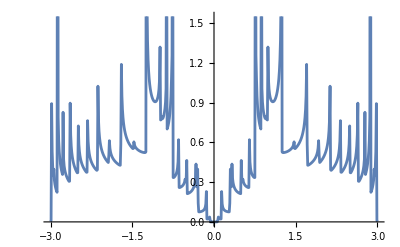

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,25][[14,14]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

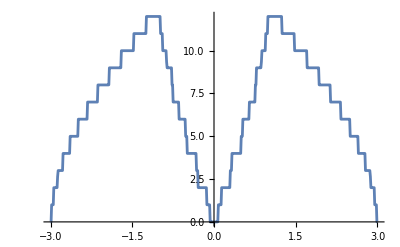

```mathematica
Table[{ω,tr[ω,0.0001,1,0,25]},{ω,Range[-3,3,0.01]}]//ListLinePlot
```

```mathematica
TLD[t_,m_]:=Module[{sizeoflead=25},Module[{mat=RandomInteger[0,{102,102}]},ReplacePart[mat,Table[{2n,50-2n+1},{n,(m-1)/2}]->t]]]
```

```mathematica
ρLD[t_,m_]:=Module[{sizeoflead=25},Module[{mat=RandomInteger[0,{102,102}]},ReplacePart[mat,Table[{2n,2n},{n,(m-1)/2}]->t]]]
```

```mathematica
ρLD[1,13]
```

```mathematica
g1[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,51]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[102]},MAT[[1;;50,1;;50]]=LEFT[ω,0.0001,1,0,25];MAT]
```

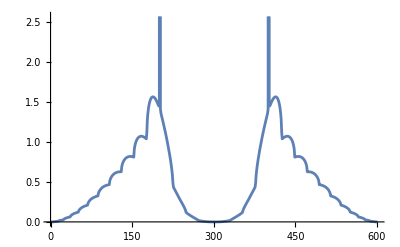

```mathematica
ListLinePlot[Table[-Im[SRLEAD[Ω,25][[1,1]]],{Ω,Range[-3,3,0.01]}]]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[102]},MAT[[1;;2m,1;;2m]]=LEFT[ω,0.0001,1,0,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=25},Inverse[IdentityMatrix[102]-g1[ω,0.0001,1,0].ConjugateTranspose[TLD[1,25]].SLLEAD[ω,25].TLD[1,25]].g1[ω,0.0001,1,0]]
```

```mathematica
f1[y_,start_,stop_]:=f1[y,start,stop]= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=s[xstart,xstop,ystart,ystop]=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25],s[1,50,75,102](*,s[38,50,38,50]*)],concentration],RandomSample[Join[s[1,50,26,74](*,s[38,50,1,37]*)],total-concentration]],First],10000]
```

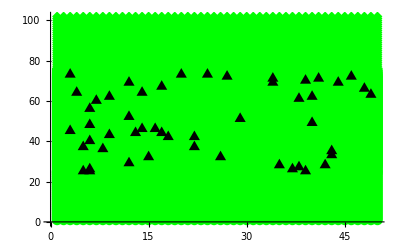

```mathematica
ListPlot[{s[1,50,1,25],s[1,50,26,74],s[1,50,75,102],dist[50,0][[515]]},PlotStyle->{Green,Green,Green,Black},PlotMarkers->Automatic]
```

```mathematica
dist[50,20][[1]]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Module[{J=β[ω,δ,t,ϵ,51],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,m_,total_,concentration_,number_]:=Module[{SSL=SRLEAD[ω,25],Tin=T1[1,51],T=ρLD[1,25],abc=dist[total,concentration][[number]]},
sl1= Module[{J1=device1[ω]},
Do[
J1=Inverse[IdentityMatrix[2*m]-Inverse[f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number]].ConjugateTranspose[Tin].J1.Tin].Inverse[f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number]],{unitcell,50}];J1=J1];
Il1:=Inverse[IdentityMatrix[2*m]-sl1.T.SSL.T].sl1;
Ir1:=Inverse[IdentityMatrix[2*m]-SSL.T.sl1.T].SSL;
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:=SSL.T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
tra=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];
{tra,If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,25],tr[ω,0.0001,1,0,25],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]}]
```

```mathematica
Mean[ParallelTable[CA[1,0.0001,1,0,1,51,50,20,n][[2]],{n,500}]]
```

4.35772

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_"<>ToString[x]<>"_.dat",Print[x];Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,51,50,x,n][[2]],{n,500}]]},{ω,Range[-3,3,0.01]}]],{x,Range[10,40,5]}]
```

10

15

20

25

35

40

{/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_10_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_15_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_20_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_25_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_30_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_35_.dat,/home/shardulmukim/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_40_.dat}

```mathematica
transmission:= Table[{x,Import["~/PhD/fwi/AGNR/sudo_q/CA_HALF_DEVICE_25agnr_50imp_lead_25agnr_sameside_"<>ToString[x]<>"_.dat"]},{x,Range[10,40,5]}]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,m_,total_,concentration_,number_]
```

```mathematica
input=Table[ParallelTable[{ω,CA[ω,0.0001,1,0,1,51,50,25,n][[2]]},{ω,Range[-3,3,0.01]}],{n,10}]
```

{1}
 |  |  |  |

```mathematica
Dimensions[transmission[[1,2]]]
```

{601,2}

```mathematica
Range[0,6,0.01]//Dimensions
```

{601}

```mathematica
misfit[x_,y_,n_]:=misfit[x,y,n]=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{Range[0,6,0.01],(m5[[1;;601,2]]-transmission[[con,2]][[1;;601,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,7}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{Transpose[ρ1][[2]],lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Clear[misfit]
```

```mathematica
misfit[6,0,1]
```

{{0.00882983,0.0089869,0.00906378,0.00917734,0.00945547,0.0098137,0.00978731},{10,0.00882983}}

```mathematica
Clear[b]
```

```mathematica
d2[x_,n_]:=Median[ParallelTable[misfit[x,y,n][[2]],{y,0.15,x-0.01,0.1}]]
```

```mathematica
Mean[Table[d2[x,1],{x,Range[0.5,6,0.1]}]]
```

{1533504988977081812640499283/108535976245504995050223360,0.00938378}

```mathematica
N[%47[[1]]]
```

14.129

```mathematica
Monitor[Table[Median[Table[d2[x,n],{x,Range[0.5,6,0.1]}]],{n,10}],n]//N
```

```mathematica
b[X_,n_]:=ParallelTable[misfit[X+delta,X,n][[2]][[1]],{delta,Range[0.1,6-X-0.01,0.04]}]
```

```mathematica
Dimensions[b[1,1]]
```

{123}

```mathematica
Table[{y,(*Histogram[b[y,2]]*)Mean[b[y,1]]},{y,Range[0.01,5.7,0.1]}]//N
```

{{0.01,13.0068},{0.11,13.3793},{0.21,13.9161},{0.31,14.2143},{0.41,14.9275},{0.51,15.8889},{0.61,16.6917},{0.71,16.5},{0.81,15.7031},{0.91,14.32},{1.01,14.1463},{1.11,13.},{1.21,13.178},{1.31,12.913},{1.41,12.3894},{1.51,11.5909},{1.61,11.2963},{1.71,11.8095},{1.81,11.4563},{1.91,10.85},{2.01,10.2041},{2.11,10.},{2.21,10.},{2.31,10.},{2.41,10.1136},{2.51,10.},{2.61,10.5422},{2.71,11.0625},{2.81,11.3462},{2.91,11.3333},{3.01,11.8493},{3.11,11.8571},{3.21,11.5441},{3.31,11.2308},{3.41,10.},{3.51,10.},{3.61,10.6034},{3.71,10.},{3.81,10.},{3.91,12.2},{4.01,14.375},{4.11,23.1111},{4.21,18.6047},{4.31,19.75},{4.41,15.1316},{4.51,10.8571},{4.61,10.},{4.71,10.},{4.81,10.},{4.91,10.},{5.01,13.4783},{5.11,13.},{5.21,18.6111},{5.31,15.6667},{5.41,21.9231},{5.51,18.5},{5.61,22.8571}}

```mathematica
Transpose[Join[{Range[1,21,1]},{Abs[Table[Print[n];N[Mean[Abs[Flatten[Table[Print["Y="<>ToString[Y]<>"."];b[Y,n],{Y,Range[0.01,5.7,0.1]}]]]]],{n,1}]]}]]
```

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{12.8465}} cannot be transposed.

Transpose[{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{12.8465}}]

```mathematica
ListLinePlot[transmission]
```

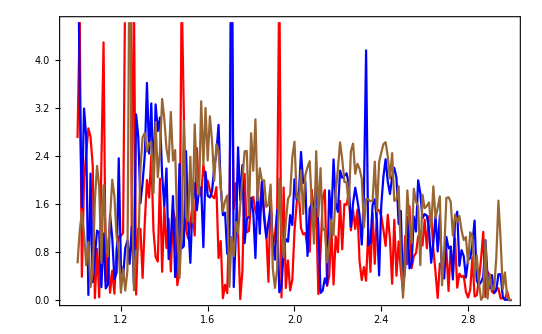

```mathematica
ListLinePlot[{ParallelTable[{ω,CA[ω,0.0001,1,0,1,51,100,50,4][[2]]},{ω,Range[1,3,0.01]}],ParallelTable[{ω,CA[ω,0.0001,1,0,1,51,50,25,4][[2]]},{ω,Range[1,3,0.01]}],ParallelTable[{ω,CA[ω,0.0001,1,0,1,51,25,15,4][[2]]},{ω,Range[1,3,0.01]}]},PlotStyle->{Red,Blue,Brown},Frame->True]
```

```mathematica
Manipulate[Show[%41,FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[0,4,1],None},{Range[0,3,0.5],None}},Epilog->{Dynamic[If[True,Locator[Dynamic[pt],%43,ImageSize->250],{}]]}],{pt,Scaled[{0.5,0.5}],None}]
```

```mathematica
Manipulate[Show[ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,51,100,50,4][[2]]},{ω,Range[1,3,0.01]}],Frame->True,PlotRange->{{0,3},{0,5}},Epilog->{Dynamic[If[True,Locator[Dynamic[pt],%43,ImageSize->250],{}]]},PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},FrameTicks->{{Range[5,20,5],None},{Automatic,None}}],ListLinePlot[Table[{ω,CA[ω,0.0001,1,0,1,51,50,3.,4][[2]]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->{Gray},PlotRange->{{0,3},{0,25}}],FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]},ImageSize->500],{pt,Scaled[{0.5,0.5}],None}]
```

```mathematica
Table[Mean[ParallelTable[CA[1.55,0.0001,1,0,1,51,x,x/2,n],{n,500}]],{x,Range[10,100,10]}]
```

{{3.6521,3.6521},{3.04147,3.04147},{2.66482,2.66482},{2.40814,2.40814},{2.19638,2.19638},{2.01589,2.01589},{1.89758,1.89758},{1.72978,1.72978},{1.58634,1.58634},{1.44778,1.44778}}

```mathematica
Transpose[%61][[1]]
```

{3.6521,3.04147,2.66482,2.40814,2.19638,2.01589,1.89758,1.72978,1.58634,1.44778}

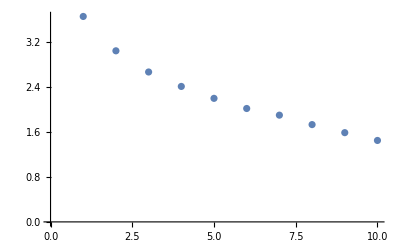

```mathematica
ListPlot[{3.6520996048185945,3.0414693873424166,2.6648193434772423,2.4081448713661286,2.196376105171992,2.015889479982517,1.8975849122957293,1.7297807028786192,1.5863425425869824,1.4477843549417673}]
```

```mathematica
21.02/4*14
```

73.57